# WORKING WITH TABULAR DATA

## DR JHK @ THE GEORGE WASHINGTON UNIVERSITY

## WHO IS THIS TUTORIAL FOR

You are fairly new to the Wolfram Language, but have experience in data science using Python or R

You are an experienced user of the Wolfram Language and want to learn of Tabular objects

## WHY USE THE WOLFRAM LANGAUGE FOR DATA SCIENCE

Why not use free open-source software

It is free to you, but affords the developers of open-source packages very little

Corporations and companies make billions of dollars from software written by open-source languages and the developers of packages for those languages get very little in return

It is absolutely necessary to advocate that developers of open-source packages be compensated for their efforts

Salary

Time

Academic or other recognition

Why use the Wolfram Language

It is undeniably a great, modern computer language

Tools are included

Developers at Wolfram Research earn a living

## WHAT WILL YOU LEARN IN THIS TUTORIAL

Introduction to Tabular objects

Why use Tabular objects instead of Lists, Associations, or Datasets

Generating Tabular objects

Inspecting Tabular objects once created to ensure data integrity

Indexing using rows and columns

Subsetting

Manipulating the content of a Tabular object

Summary statistics and data visualization of a Tabular object

## REASONS TO USE TABULAR DATA

Watch the Wolfram U course on Tabular objects at  https://www.wolfram.com/wolfram-u/courses/data-science/tabular-efficient-data-processing-dat904/

Tabular objects are similar to Pandas DataFrame objects in Python and Tibble object in the tidyverse dialect of R

Consider the following

Tabular objects are still considered experimental and additions and improvements are planned

Tabular objects were introduced in version

There are several reasons use Tabular objects

### GENERATE DATA TO EXPLORE REASONS TO USE TABULAR OBJECTS

Generate  random dates

```mathematica
(*Generate 100000 random dates and assign the result to the variable dates*)
dates=RandomDate[100000];
```

```mathematica
(*Return the data type of dates*)
Head[dates]
```

List

The TabularColumn function takes a List object as parameter and returns a table with a single column

```mathematica
(*Convert dates to Tabular format and assign the result to the variable datesColumn*)
datesColumn=TabularColumn[dates];
```

```mathematica
(*Return the data type of datesFColumn*)
Head[datesColumn]
```

TabularColumn

### MEMORY ALLOCATION

Tabular objects are more memory efficient than List objects

The ByteCount function return the number of bytes required to store an object

```mathematica
(*Return the number of bytes in the dates List object*)
ByteCount[dates]
```

35200080

```mathematica
(*Return the number of bytes in the datesColumn object*)
ByteCount[datesColumn]
```

800680

### SPEED

The RepeatedTiming function evaluates an expression multiple times and returns an average time to completion

The Mean function calculates the mean

```mathematica
(*Calculate the average time to calculate the mean of the date List object*)
RepeatedTiming[Mean[dates]]
```

{0.112324,Thu 2 Jul 2026 06:08:55GMT-4}

```mathematica
(*Calculate the times it takes to calculate the mean date of the TabularColumn object*)
RepeatedTiming[Mean[datesColumn]]
```

{4.74468×10^-6,Thu 2 Jul 2026 06:08:55GMT-4}

```mathematica
(*Clear the variables from memory*)
Clear[dates]
Clear[datesColumn]
```

## RESOUCES

The notebook in this version was generated using Mathematica version 15.0.1.0

The notebook and the data file are available in the description of this video

No artificial intelligence was used to generate any part of this notebook

## GENERATING TABULAR OBJECTS

Tabular objects can be generated from many other objects

### TABULAR OBJECTS FROM LISTS

Generating a table of data from a nested List object as parameters of the Tabular function

First nested List contains Lists of row-wise data

Second list contains column names

```mathematica
(*Rows and columns as a nested List object (row-by-row) and assign it to the variable data*)
data=Tabular[{{1,"Anne",DateObject[{2027,10,11}],22},{2,"Mary",DateObject[{2027,10,12}],33},{3,"Kate",DateObject[{2027,10,11}],44},{4,"Bella",DateObject[{2027,12,12}],55}},{"ID","Name","Date","Age"}]
```

A Tabular object can be converted to a normal expression using the Normal function

The normal expression of a Tabular object is a List of Associations

```mathematica
(*Return the tabular object as a List of Associations*)
Normal[data]
```

{<|ID→1,Name→Anne,Date→Mon 11 Oct 2027,Age→22|>,<|ID→2,Name→Mary,Date→Tue 12 Oct 2027,Age→33|>,<|ID→3,Name→Kate,Date→Mon 11 Oct 2027,Age→44|>,<|ID→4,Name→Bella,Date→Sun 12 Dec 2027,Age→55|>}

### TABULAR OBJECTS FROM A LIST OF ASSOCIATIONS

Since the normal expression of a Tabular object is a List of Associations, we can generate a Tabular object from a List of Associations

```mathematica
(*Generate a List of Association objects and assign it to the variable assc*)
assc={<|"ID"->1,"Name"->"Anne","Date"->DateObject[{2027,10,11}],"Age"->22|>,<|"ID"->2,"Name"->"Mary","Date"->DateObject[{2027,10,12}],"Age"->33|>,<|"ID"->3,"Name"->"Kate","Date"->DateObject[{2027,10,11}],"Age"->44|>,<|"ID"->4,"Name"->"Bella","Date"->DateObject[{2027,12,12}],"Age"->55|>}
```

{<|ID→1,Name→Anne,Date→Mon 11 Oct 2027,Age→22|>,<|ID→2,Name→Mary,Date→Tue 12 Oct 2027,Age→33|>,<|ID→3,Name→Kate,Date→Mon 11 Oct 2027,Age→44|>,<|ID→4,Name→Bella,Date→Sun 12 Dec 2027,Age→55|>}

```mathematica
(*Generate a Tabular object from the List of Associations*)
Tabular[assc]
```

### TABULAR OBJECTS FROM CSV FILES

Tabular objects can be generated by importing spreadsheet files using the Import function and specifying Tabular as the object type

```mathematica
(*Import the eda_full.csv file and assig it to the variable tab*)
tab=Import["/Users/jayklopper/Documents/Wolfram/TabularData/eda_full.csv","Tabular"]
```

### TABULAR OBJECT FROM THE WOLFRAM DATA REPOSITORY

Visit the Wolfram Data Repository and search for Sample Tabular Data

```mathematica
(*Import the Health Expenditure data set and assign it to the variable health*)
health=ResourceData["Sample Tabular Data: Health Expenditure"]
```

## INSPECTING A TABULAR OBJECT

When a Tabular object is generated (especially when the data is imported from a spreadsheet or similar data formats), it is good practice to inspect the object for any data errors

### INSPECT THE NUMBER OF OBSEREVATIONS AND VARIABLES

Assuming that the data is in long-from tidy data format, we can determine the number of observations (rows) and the number of variables (columns)

The Dimensions function return a List object with the number of rows and columns in a Tabular object

```mathematica
(*Return the dimensions of tab*)
Dimensions[tab]
```

{100,20}

The Length function return the number of rows in a Tabular object

```mathematica
(*Return the number of rows in tab*)
Length[tab]
```

100

The ColumnKeys function return a List of all the column headers in a Tabular object and the Length object returns the number of these column headers

```mathematica
(*Return the number of columns in tab*)
Length[ColumnKeys[tab]]
```

20

### COLUMNS

The ColumnKeys function return the column names

```mathematica
(*Return the column header names*)
ColumnKeys[tab]
```

{patient_id,visit_date,age_months,age_group,sex,weight_kg,height_cm,bmi,head_circumference_cm,temperature_c,heart_rate_bpm,respiratory_rate_bpm,spo2_pct,systolic_bp_mmhg,diastolic_bp_mmhg,triage_category,primary_diagnosis,length_of_stay_hours,discharge_status,readmitted_within_7_days}

The ColumnTypes function returns the data type of observations in each column

```mathematica
(*Return the column data types*)
ColumnTypes[tab]
```

<|patient_id→String,visit_date→String,age_months→Integer64,age_group→String,sex→String,weight_kg→Real64,height_cm→Real64,bmi→Real64,head_circumference_cm→Real64,temperature_c→Real64,heart_rate_bpm→Integer64,respiratory_rate_bpm→Integer64,spo2_pct→Integer64,systolic_bp_mmhg→Integer64,diastolic_bp_mmhg→Integer64,triage_category→String,primary_diagnosis→String,length_of_stay_hours→Real64,discharge_status→String,readmitted_within_7_days→String|>

### EXAMINING THE STRUCTURE OF TABULAR OBJECTS

A Tabular object determines the level of measurement of the observations in each column

The ColumnTypes function returns the Wolfram Language data type for the observations in each column

```mathematica
(*Return the data type of the observations in the tab tabular object*)
ColumnTypes[tab]
```

<|patient_id→String,visit_date→String,age_months→Integer64,age_group→String,sex→String,weight_kg→Real64,height_cm→Real64,bmi→Real64,head_circumference_cm→Real64,temperature_c→Real64,heart_rate_bpm→Integer64,respiratory_rate_bpm→Integer64,spo2_pct→Integer64,systolic_bp_mmhg→Integer64,diastolic_bp_mmhg→Integer64,triage_category→String,primary_diagnosis→String,length_of_stay_hours→Real64,discharge_status→String,readmitted_within_7_days→String|>

Inspecting the structure of a Tabular object helps in identifying data entry errors such as missing data or incorrect levels of measurement

The TabularStructure function returns the data type, non-missing count, missing count, and the byte count of each column by default

```mathematica
(*Return the structure of the tab Tabular object*)
TabularStructure[tab]
```

Two other properties are also available

```mathematica
(*Return the DuplicateFreeQ, the CountDistinct, and the MissingProxy properties of the structure of the tab Tabular object*)
TabularStructure[tab,All,{"DuplicateFreeQ","CountDistinct","MissingProxy"}]
```

Use the All keyword to return all the properties for all the columns

```mathematica
(*Return all the properties*)
TabularStructure[tab,All,All]
```

## INDEXING

Indexing allows us to identify and extract certain rows, columns, or individual observations

### RETURN ROWS

Indexing is performed using bracket notation, either single or double square brackets

Using a single index number returns a TabularRow object

```mathematica
(*Return the first row as a TabularRow object using double bracket notation*)
tab[[1]]
```

TabularRow[…]

```mathematica
(*Single bracket notation*)
tab[1]
```

TabularRow[…]

The Normal function returns an Association object

```mathematica
(*Return the first row as an Association*)
Normal[tab[1]]
```

<|patient_id→PED001,visit_date→01-13,age_months→164,age_group→adolescent,sex→Male,weight_kg→57.5,height_cm→155.5,bmi→23.8,head_circumference_cm→54.3,temperature_c→37.9,heart_rate_bpm→77,respiratory_rate_bpm→13,spo2_pct→97,systolic_bp_mmhg→117,diastolic_bp_mmhg→79,triage_category→4 – Semi-urgent,primary_diagnosis→Asthma exacerbation,length_of_stay_hours→3.5,discharge_status→Admitted to ward,readmitted_within_7_days→No|>

Negative index values return rows from the end of the Tabular object

```mathematica
(*Return the last row as an Association*)
Normal[tab[[-1]]]
```

<|patient_id→PED100,visit_date→11-25,age_months→128,age_group→school,sex→Female,weight_kg→40.8,height_cm→131.3,bmi→23.7,head_circumference_cm→52.5,temperature_c→36.3,heart_rate_bpm→89,respiratory_rate_bpm→21,spo2_pct→99,systolic_bp_mmhg→108,diastolic_bp_mmhg→60,triage_category→3 – Urgent,primary_diagnosis→Asthma exacerbation,length_of_stay_hours→5.1,discharge_status→Admitted to ward,readmitted_within_7_days→No|>

A List of row values can be used as index

```mathematica
(*Return rows 1, 3, and 5 as a List of Associations*)
Normal[tab[{1,3,5}]]
```

{<|patient_id→PED001,visit_date→01-13,age_months→164,age_group→adolescent,sex→Male,weight_kg→57.5,height_cm→155.5,bmi→23.8,head_circumference_cm→54.3,temperature_c→37.9,heart_rate_bpm→77,respiratory_rate_bpm→13,spo2_pct→97,systolic_bp_mmhg→117,diastolic_bp_mmhg→79,triage_category→4 – Semi-urgent,primary_diagnosis→Asthma exacerbation,length_of_stay_hours→3.5,discharge_status→Admitted to ward,readmitted_within_7_days→No|>,<|patient_id→PED003,visit_date→10-02,age_months→187,age_group→adolescent,sex→Female,weight_kg→77.2,height_cm→179.,bmi→24.1,head_circumference_cm→54.7,temperature_c→38.,heart_rate_bpm→65,respiratory_rate_bpm→12,spo2_pct→97,systolic_bp_mmhg→123,diastolic_bp_mmhg→86,triage_category→5 – Non-urgent,primary_diagnosis→Urinary tract infection,length_of_stay_hours→2.5,discharge_status→Admitted to ward,readmitted_within_7_days→No|>,<|patient_id→PED005,visit_date→12-17,age_months→143,age_group→school,sex→Male,weight_kg→25.8,height_cm→153.3,bmi→11.,head_circumference_cm→53.7,temperature_c→38.2,heart_rate_bpm→93,respiratory_rate_bpm→17,spo2_pct→100,systolic_bp_mmhg→112,diastolic_bp_mmhg→53,triage_category→3 – Urgent,primary_diagnosis→Upper respiratory tract infection,length_of_stay_hours→3.7,discharge_status→Admitted to ICU,readmitted_within_7_days→No|>}

After importing a data set as a Tabular object, it is useful to return the first couple of rows of data to make sure the spreadsheet imported correctly

```mathematica
(*Return the first 5 rows of tab as a Tabular object*)
tab[1;;5]
```

The Take function can be used to return the first  rows

```mathematica
(*return the first 5 rows of the tab Tabular object*)
Take[tab,5]
```

### RETURN COLUMNS

When an index contains a comma, the indexing is by row and then column

A TabularColumn object is returned

```mathematica
(*Return all the rows in the first column of tab*)
tab[[All,1]]
```

TabularColumn[…]

The Normal function return a List of values

```mathematica
(*Return a List of values for the first column*)
Normal[tab[All,1]]
```

{PED001,PED002,PED003,PED004,PED005,PED006,PED007,PED008,PED009,PED010,PED011,PED012,PED013,PED014,PED015,PED016,PED017,PED018,PED019,PED020,PED021,PED022,PED023,PED024,PED025,PED026,PED027,PED028,PED029,PED030,PED031,PED032,PED033,PED034,PED035,PED036,PED037,PED038,PED039,PED040,PED041,PED042,PED043,PED044,PED045,PED046,PED047,PED048,PED049,PED050,PED051,PED052,PED053,PED054,PED055,PED056,PED057,PED058,PED059,PED060,PED061,PED062,PED063,PED064,PED065,PED066,PED067,PED068,PED069,PED070,PED071,PED072,PED073,PED074,PED075,PED076,PED077,PED078,PED079,PED080,PED081,PED082,PED083,PED084,PED085,PED086,PED087,PED088,PED089,PED090,PED091,PED092,PED093,PED094,PED095,PED096,PED097,PED098,PED099,PED100}

A column can also be called by its name

```mathematica
(*Return the age_months column as a List object*)
Normal[tab[[All,"age_months"]]]
```

{164,108,187,98,143,37,109,185,29,55,9,187,141,201,136,67,90,28,68,11,86,50,153,94,192,169,162,32,67,107,214,7,21,56,51,108,83,143,122,151,73,31,68,151,70,194,170,114,30,18,83,152,173,43,37,78,191,9,192,192,30,26,32,38,135,103,111,40,185,210,192,114,196,81,21,45,121,142,113,39,190,190,73,206,210,121,160,18,87,140,178,177,156,72,45,52,19,43,149,128}

More than one column can be specified as a List

```mathematica
(*Return the age_months and sex columns*)
tab[All,{"age_months","sex"}]
```

### RETURN A SINGLE DATA POINT

A single data point can be returned using the row-comma-column index notation

```mathematica
(*Return the sex of the fourth subject*)
tab[4,"sex"]
```

Female

## SUBSETTING

We can use comparison operators to extract only specified data from a Tabular object

### SUBSETS

The Select function is used to select a subset of data in a Tabular object

A Function is used to subset the data

```mathematica
(*Select only Female subjects from the sex column*)
Select[tab,Function[#sex=="Female"]]
```

```mathematica
(*Return the rows where the age_months is at least 200*)
Select[tab,Function[#"age_months">=200]]
```

The && symbol indicates the logical And connective

```mathematica
(*Select only females at least 200 months old*)
Select[tab,Function[#sex=="Female"&&#"age_months">=200]]
```

```mathematica
(*Use the And function as alternative syntax*)
Select[tab,Function[And[#sex=="Female",#"age_months">=200]]]
```

The || operator indicates the logical Or connective

```mathematica
(*Select either females or subjects at least 200 months old*)
Select[tab,Function[#sex=="Female"||#"age_months">=200]]
```

```mathematica
(*Use the Or function as alternative syntax*)
Select[tab,Function[Or[#sex=="Female",#"age_months">=200]]]
```

Use the ≠ symbol or the logical Not connective or the Discard function

```mathematica
(*Select only subjects that are not adolescent*)
Select[tab,Function[#"age_group"!="adolescent"]]
```

```mathematica
(*Use the logical Not function as alternative syntax*)
Select[tab,Function[Not[#"age_group"=="adolescent"]]]
```

```mathematica
(*Use the Discard function to remove all rows where the age_group is adolescent*)
Discard[tab,Function[#"age_group"=="adolescent"]]
```

### SUBSET AND SPECIFY COLUMNS TO DISPLAY

We can subset by comparison and then display specific columns

```mathematica
(*Use the Discard function to remove all rows where the age_group is adolescent and then only show the patient_id and age_group columns*)
Discard[tab,Function[#"age_group"=="adolescent"]][All,{"patient_id","age_group"}]
```

### SUBSETS BY INDEXING

When observations are not unique add more than one column as index

In the health Tabular object the Country and Year columns contain non-unique values

```mathematica
(*Return the first five rows of health*)
health[1;;5]
```

Combining them as keys generate unique combinations using the KeyColumns key

```mathematica
(*Create a new Tabular object by selecting Country and Year to be indices and assign the result to the variable healthIndex*)
healthIndex=Tabular[health,<|"KeyColumns"->{"Country","Year"}|>]
```

Now use the RowKey function to search for a specific row

```mathematica
(*Return the column keys and data types for the row Canada in the year 2000*)
healthIndex[RowKey[{"Canada",2000}]]
```

TabularRow[…]

```mathematica
(*Use Normal to return an Association object for the desired row*)
Normal[healthIndex[RowKey[{"Canada",2000}]]]
```

<|Country→Canada,Year→2000,LifeExpectancy→79.233,TotalHealthExpenditure→3007.38|>

## DATA WRANGLING

Data wrangling considers changes that can be made to a Tabular object before or during data analysis

### SORTING

All observations (rows) can be sorted by the values in a particular column using the SortBy function

```mathematica
(*Sort by age_months in default ascending order*)
SortBy[tab,"age_months"]
```

Sort in descending order using the ReverseSortBy function

```mathematica
(*Sort in descending order*)
ReverseSortBy[tab,"age_months"]
```

```mathematica
(*Sort by age_months and then weight_kg in descending order*)
ReverseSortBy[tab,{"age_months","weight_kg"}]
```

We can use the TakeLargestBy function to select only the largest  observations for a specified column

```mathematica
(*Select the five largest age_months values*)
TakeLargestBy[tab,Function[#"age_months"],5]
```

The same applies to the TakeSmallestBy function

```mathematica
(*Select the five smallest age_months values*)
TakeSmallestBy[tab,Function[#"age_months"],5]
```

The MinimalBy and MaximalBy functions returns the observations with the smallest and largest observation for a specific column respectively

```mathematica
(*Return the observation with the smallest age*)
MinimalBy[tab,"age_months"]
```

```mathematica
(*Return the observation with the greatest age*)
MaximalBy[tab,"age_months"]
```

### ADDING COLUMNS

Add a column based on the values in another column(s)

Add a column named  based on the values in the column

```mathematica
(*Add a new column named WeighClass with True if weight_kg is at least 50 and False if not*)
TransformColumns[tab,"WeightClass"->Function[#"weight_kg">=50]]
```

Add a column named   with weight in pounds

Add it directly after the  column instead of at the end

```mathematica
(*Add as new column named weight_lbs with weight in pounds based on weight_kg column*)
TransformColumns[tab,{"weight_kg","weight_lbs"->Function[#"weight_kg" 2.21]}]
```

Combine the previous two column operations

```mathematica
(*Combine the addition of the two new columns above*)
TransformColumns[tab,{"weight_kg","WeightClass"->Function[#"weight_kg">=50],"weight_lbs"->Function[#"weight_kg" 2.21]}]
```

Standardize the values of a column using the ColumnwiseValue function to generate a new column named

```mathematica
(*Standardize the wight_kg column and add the values as a new columns named StandardizedWeight after the weight_kg column*)
TransformColumns[tab,{"weight_kg","StandardizedWeight"->Function[(#"weight_kg"-ColumnwiseValue[Mean[#"weight_kg"]])/ColumnwiseValue[StandardDeviation[#"weight_kg"]]]}]
```

Add a new column with data using the InsertColumn function

```mathematica
(*Generate a List with 100 random observations from the sample space Group A, Group B, and Group C, and assign the result to the variable groups*)
groups=RandomChoice[{"Group A","Group B","Group C"},100]
```

{Group A,Group A,Group A,Group B,Group C,Group B,Group C,Group C,Group B,Group B,Group B,Group A,Group C,Group A,Group A,Group B,Group C,Group C,Group A,Group A,Group A,Group C,Group C,Group A,Group A,Group C,Group A,Group B,Group B,Group C,Group C,Group B,Group A,Group A,Group C,Group C,Group B,Group C,Group B,Group A,Group C,Group A,Group B,Group B,Group B,Group B,Group A,Group C,Group A,Group A,Group A,Group A,Group B,Group A,Group B,Group B,Group C,Group A,Group A,Group C,Group C,Group C,Group C,Group B,Group B,Group C,Group B,Group B,Group C,Group B,Group B,Group C,Group C,Group B,Group A,Group B,Group A,Group A,Group C,Group C,Group C,Group A,Group B,Group A,Group C,Group B,Group C,Group C,Group A,Group C,Group B,Group A,Group C,Group B,Group B,Group C,Group B,Group A,Group C,Group B}

```mathematica
(*Generate a new column named Groups that contains the List of values in groups and insert it after the patient_id column*)
InsertColumns[tab,{"patient_id","Groups"->groups}]
```

### DELETING COLUMNS

Delete columns using the DeleteColumns function

```mathematica
(*Delete the patient_id column*)
DeleteColumns[tab,"patient_id"]
```

### CHANGING COLUMN TYPE

We can use the CastColumns function to change the data type of observations in a specific column

```mathematica
(*Change the vist_date from a String to a Date type and save the changes*)
tab=CastColumns[tab,"visit_date"->"Date"]
```

```mathematica
(*Verify the change using the ColumnTypes function*)
ColumnTypes[tab]
```

<|patient_id→String,visit_date→Date::[Integer32,Day,Gregorian,None],age_months→Integer64,age_group→String,sex→String,weight_kg→Real64,height_cm→Real64,bmi→Real64,head_circumference_cm→Real64,temperature_c→Real64,heart_rate_bpm→Integer64,respiratory_rate_bpm→Integer64,spo2_pct→Integer64,systolic_bp_mmhg→Integer64,diastolic_bp_mmhg→Integer64,triage_category→String,primary_diagnosis→String,length_of_stay_hours→Real64,discharge_status→String,readmitted_within_7_days→String|>

### DECODING

When data is captured, it is often encoded with numbers

The data can be decoded using Rule objects

```mathematica
(*Generate Tabular object and assign to the variable decode*)
decode=Tabular[{<|"ID"->1,"Group"->1|>,<|"ID"->2,"Group"->2|>}]
```

```mathematica
(*Generate a List of Rule objects to decode the elemenmts in the Group column with 1 decoded as Group 1 and 2 decoded as Group 2, and assign the result to the variable rule*)
rule={1->"Group 1",2->"Group 2"}
```

{1→Group 1,2→Group 2}

```mathematica
(*Decode the data in the Group column using the ReplaceAll function*)
TransformColumns[decode,"Group"->Function[ReplaceAll[#Group,rule]]]
```

### PIVOT TABLES

It can be convenient to summarize categorical data using pivot tables

```mathematica
(*Calculate the number of cases of each age group for each readmission status group*)
PivotTable[tab,Function[Length[#sex]],"sex","readmitted_within_7_days"]
```

We can also calculate summary statistics in a pivot table

```mathematica
(*Calculate the mean age for the pivot table above*)
PivotTable[tab,Function[Mean[#"age_months"]],"sex","readmitted_within_7_days"]
```

### MISSING DATA

Data imputation and interpolation are available for missing data

Imputation is the general process of replacing missing data points with substituted values, while interpolation is a specific technique that estimates missing values by constructing new points between known data points

```mathematica
(*Generate a Tabular object with missing data and assign the result to the variable missing*)
missing=Tabular[{{1,1,Missing[],3,4},{2,Missing[],3,4,2},{3,1,2,3,2},{4,1,1,Missing[],Missing[]},{1,1.2,3,2,1.3}},{"ID","A","B","C","D"}]
```

```mathematica
(*Return the structure to inspect the missing count*)
TabularStructure[missing]
```

The type of interpolation can be specified for all columns or specified per column using the TransformMissing function

```mathematica
(*Linear interpolation (default)*)
TransformMissing[missing,"Interpolation"]
```

```mathematica
(*Previous element interpolation as PreviousElement*)
TransformMissing[missing,"PreviousElement"]
```

```mathematica
(*Next element interpolation as NextElement*)
TransformMissing[missing,"NextElement"]
```

```mathematica
(*Specify the mean imputation for A and the NearestElement interpolation for B*)
TransformMissing[missing,{"A"->"Mean","B"->"NearestElement"}]
```

Values can be imputed based on a distribution

```mathematica
(*Calculate the mean and the standard deviation of values in column A and assign the results to the variables meanA and stdA*)
meanA=Mean[DeleteMissing[Normal[missing[All,"A"]]]]
stdA=StandardDeviation[DeleteMissing[Normal[missing[All,"A"]]]]
```

1.05

0.1

```mathematica
(*Generate a normal distribution based on the previous mean and standard deviation and assign the result to the variable dist*)
dist=NormalDistribution[meanA,stdA]
```

NormalDistribution[1.05,0.1]

```mathematica
(*Specify the imputation of column A based on the distribution*)
TransformMissing[missing,"A"->{"RandomVariate",dist}]
```

A constant can be specified as imputed value

```mathematica
(*Impute the missing observations in column A with the constant √2*)
TransformMissing[missing,"A"->{"Constant",√2}]
```

A row or rows with missing data can be removed

```mathematica
(*Delete all rows with missing data*)
TransformMissing[missing,"Delete"]
```

```mathematica
(*Delete only rows in column A with missing data*)
TransformMissing[missing,{"A"->"Delete"}]
```

## SUMMARY STATISTICS AND DATA VISUALIZATION

Data can be analyzed by extracting List objects from a Tabular object

This is best for statistical tests

Data can also be summarized and visualized directly from a Tabular object

### SUMMARY STATISTICS

We can calculate simple summary statistics for all observations in a column

```mathematica
(*Calculate the mean age of all observations*)
Mean[tab[All,"age_months"]]
```

105.78

```mathematica
(*Calculate the frequency of each category in the sex column using the Counts function*)
Counts[tab[All,"sex"]]
```

<|Male→47,Female→53|>

```mathematica
(*Calculate the proportion of each category in the sex column*)
Counts[tab[All,"sex"]]/Length[tab]
```

<|Male→47/100,Female→53/100|>

```mathematica
(*Express decimal approximations for the proportions*)
N[Counts[tab[All,"sex"]]/Length[tab]]
```

<|Male→0.47,Female→0.53|>

We can also calculate comparative summary statistics

```mathematica
(*Calculate the mean age of males and females*)
AggregateRows[tab,"Mean Age"->Function[Mean[#"age_months"]],"sex"]
```

We can specify more than one statistic to calculate

```mathematica
(*Calculate the mean and standard deviation of the age_months variables for each of the unique elements in sex column*)
AggregateRows[tab,{"Mean Age"->Function[Mean[#"age_months"]],"SD Age"->Function[StandardDeviation[#"age_months"]]},"sex"]
```

Comparisons can be specified for more than one variable (column)

```mathematica
(*Calculate the mean and standard deviation of the age_months variable for each of the unique elements in sex and triage_category columns*)
AggregateRows[tab,{"Mean Age"->Function[Mean[#"age_months"]],"SD Age"->Function[StandardDeviation[#"age_months"]]},{"sex","triage_category"}]
```

### DATA VISUALIZATION

#### VARIABLES WITH A NUMERICAL LEVEL OF MEASUREMENT

A histogram visualizes the distribution of a numerical variable

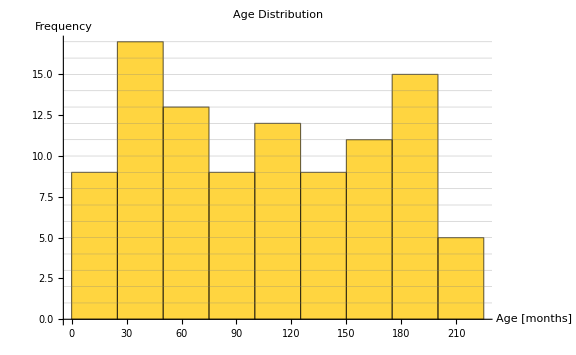

```mathematica
(*Generate a histogram of the age_months column*)
Histogram[tab->"age_months",{0,225,25},GridLines->{None,Range[1,25,1]},PlotLabel->Style["Age Distribution",14],AxesLabel->{Style["Age [months]",12],Style["Frequency",12]},ImageSize->Large]
```

The PivotToColumns add columns to a Tabular object based on specified columns

```mathematica
(*Add columns for each category of the sex column and show the age_months observations in each*)
PivotToColumns[tab,"sex"->"age_months"]
```

The result can be used to generate a stacked histogram

Be careful to note the order of the categories

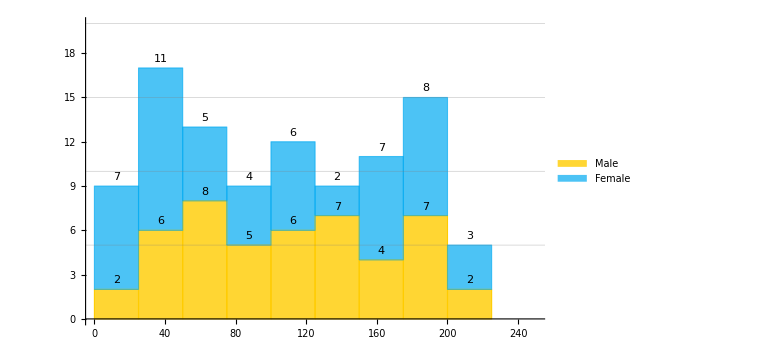

```mathematica
(*Generate stacked histogram of the age_months column for each of the categories of the sex columns*)
Histogram[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},{0,225,25},Automatic,ChartLayout->"Stacked",PlotLegends->{"Male","Female"},LabelingFunction->Above,PlotRange->{{0,250},{0,20}},GridLines->{None,Range[5,20,5]},ImageSize->Large]
```

A box-and-whisker plot is arguably better suited to visualizing the distribution of a numerical variable for different categories of a categorical variable

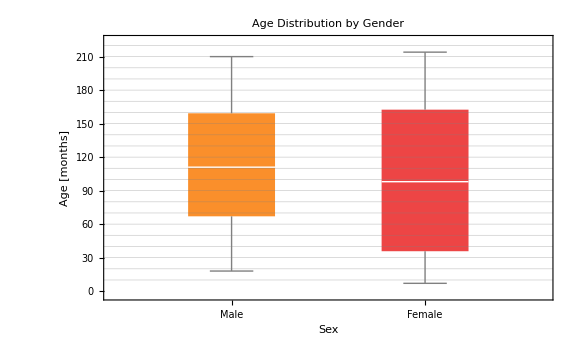

```mathematica
(*Generate a box-and-whisker plot of the age distribution of males and females*)
BoxWhiskerChart[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},"Outliers",PlotLabel->Style["Age Distribution by Gender",14],GridLines->{None,Range[10,250,10]},ImageSize->Large,PlotStyle->{StandardOrange,StandardRed},FrameLabel->{Style["Sex",14],Style["Age [months]",14]},PlotLabels->{"Male","Female"}]
```

A distribution plot can be used for similar results

There are various chart types

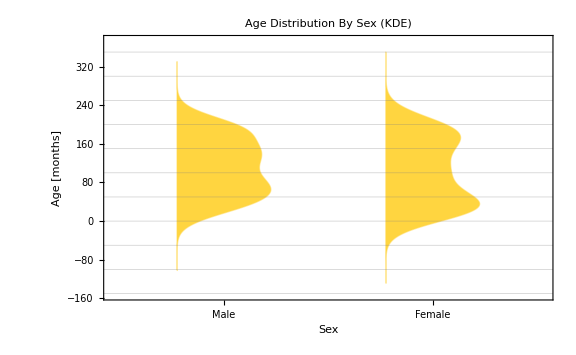

```mathematica
(*Vertical (default) distribution chart of age by sex*)
DistributionChart[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},PlotLabels->{"Male","Female"},GridLines->{None,Range[-150,350,50]},FrameLabel->{Style["Sex",12],Style["Age [months]",12]},PlotLabel->Style["Age Distribution By Sex (KDE)",14],ImageSize->Large]
```

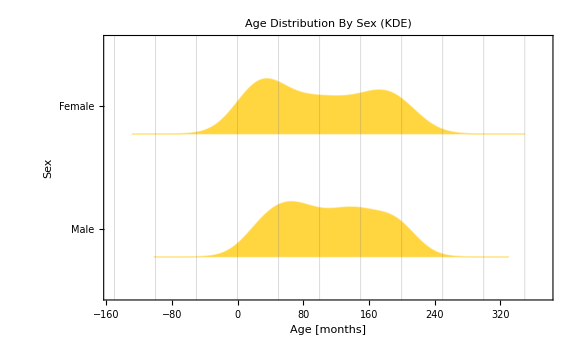

```mathematica
(*Horizontal distribution chart of age by sex*)
DistributionChart[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},PlotLabels->{"Male","Female"},GridLines->{Range[-150,350,50],None},FrameLabel->{Style["Age [months]",12],Style["Sex",12]},PlotLabel->Style["Age Distribution By Sex (KDE)",14],ImageSize->Large,BarOrigin->Left]
```

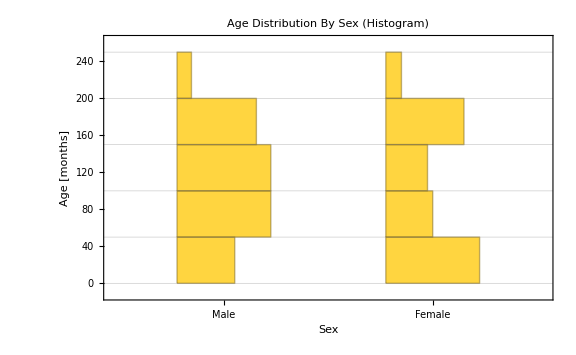

```mathematica
(*Horizontal distribution chart of age by sex as histograms*)
DistributionChart[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},"Histogram",PlotLabels->{"Male","Female"},GridLines->{None,Range[-150,350,50]},FrameLabel->{Style["Sex",12],Style["Age [months]",12]},PlotLabel->Style["Age Distribution By Sex (Histogram)",14],ImageSize->Large]
```

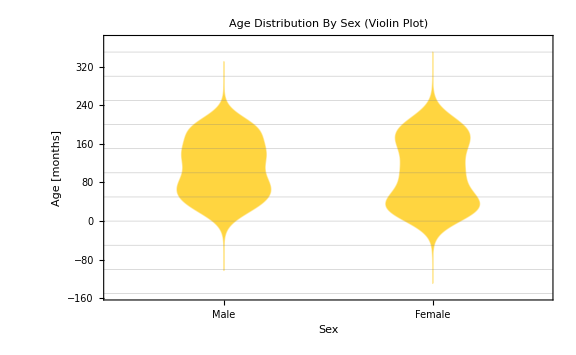

```mathematica
(*Horizontal distribution chart of age by sex as violin plots*)
DistributionChart[PivotToColumns[tab,"sex"->"age_months"]->{"Male","Female"},"Violin",PlotLabels->{"Male","Female"},GridLines->{None,Range[-150,350,50]},FrameLabel->{Style["Sex",12],Style["Age [months]",12]},PlotLabel->Style["Age Distribution By Sex (Violin Plot)",14],ImageSize->Large]
```

#### VARIABLE WITH A CATEGORICAL LEVEL OF MEASUREMENT

A bar chart visualizes the frequency of each category of a categorical variable

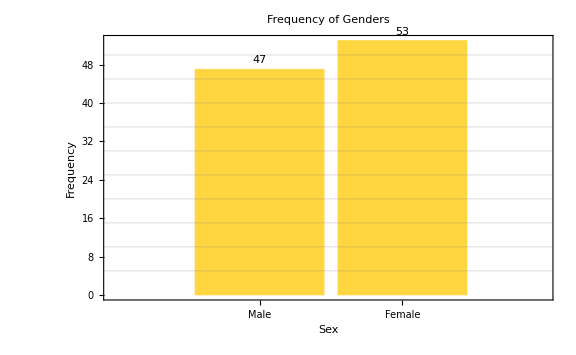

```mathematica
(*Bar chart of sex frequency*)
BarChart[Counts[tab[All,"sex"]],LabelingFunction->Above,PlotLabel->Style["Frequency of Genders",14],Frame->True(*Must be set to True for frame labels to appear*),FrameLabel->{Style["Sex",12],Style["Frequency",12]},PlotLabels->{"Male","Female"},GridLines->{None,Range[5,55,5]},ImageSize->Large]
```

As an alternative, we can create a Tabular object of the frequencies of the categories of the  column using the AggregateRows function

```mathematica
(*Create a Tabular object named sexFrequencyTable to hold the freqeuncies of each category in the sex column*)
sexFrequencyTable=AggregateRows[tab,"Frequency"->Function[Length[#sex]],"sex"]
```

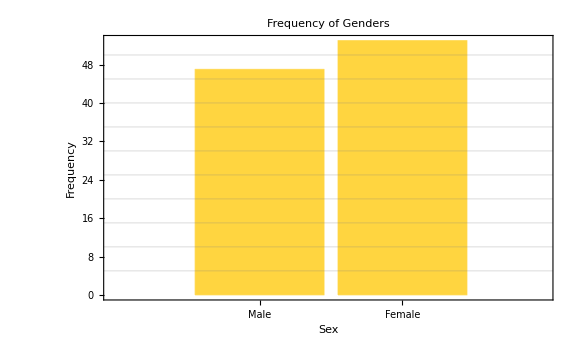

```mathematica
(*Create a bar chart using the sexFrequencyTable Tabular object*)
BarChart[sexFrequencyTable->"Frequency",PlotLabel->Style["Frequency of Genders",14],Frame->True(*Must be set to True for frame labels to appear*),FrameLabel->{Style["Sex",12],Style["Frequency",12]},PlotLabels->{"Male","Female"},GridLines->{None,Range[5,55,5]},ImageSize->Large]
```

A bar chart can also visualize the values of a contingency table (for two categorical variables)

```mathematica
(*Calculate the number of cases of each age group for each readmission status group using the PivotToColumns function and assign the result to the variable sexReadmissionContingencyTable*)
sexReadmissionContingencyTable=PivotToColumns[AggregateRows[tab,"Frequency"->Function[Length[#sex]],{"sex","readmitted_within_7_days"}],"readmitted_within_7_days"->"Frequency"]
```

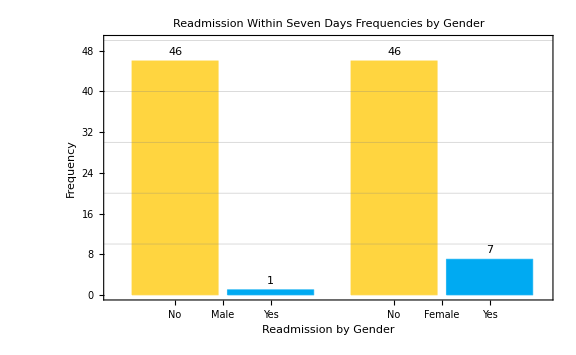

```mathematica
(*Generate a bar chart from the table above*)
BarChart[sexReadmissionContingencyTable->{"No","Yes"},PlotLabel->Style["Readmission Within Seven Days Frequencies by Gender",14],PlotLabels-><|"Groups"->{"Male","Female"},"Elements"->{"No","Yes"}|>,GridLines->{None,Range[10,50,10]},LabelingFunction->Above,Frame->True,FrameLabel->{Style["Readmission by Gender",12],Style["Frequency",12]},PlotRange->{0,50},ImageSize->Large]
```

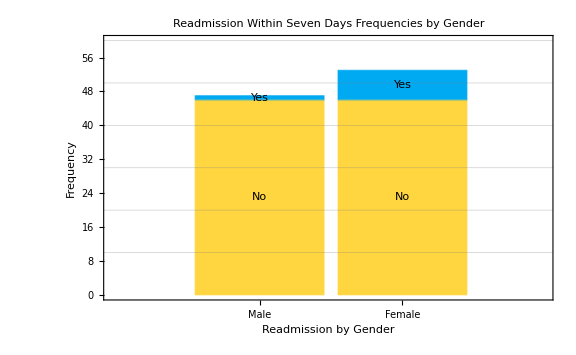

```mathematica
(*Stack the bar chart*)
BarChart[sexReadmissionContingencyTable->{"No","Yes"},PlotLabel->Style["Readmission Within Seven Days Frequencies by Gender",14],PlotLabels-><|"Groups"->{"Male","Female"},"Elements"->{"No","Yes"}|>,GridLines->{None,Range[10,60,10]},Frame->True,FrameLabel->{Style["Readmission by Gender",12],Style["Frequency",12]},PlotRange->{0,60},PlotLayout->"Stacked",ImageSize->Large]
```